## Fit student correctness to various models

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/bvds/Andes2/LogProcessing/moment-of-learning

```mathematica
data=Import["junk.csv"];
```

```mathematica
Take[data,5]
```

{{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0},{area-of-circle,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0,1},{bernoulli,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0,0,1},{combo-magnification,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0},{compo-general-case,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,1,0,0,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1}}

```mathematica
logistic[n_,{mu_,b_}]:=1/(Exp[-b  n+mu]+1); (* this choice of parameters gives finite constraint region *)
step[n_,{nl_,pg_,ps_}]:=pg+(Sign[n-nl+1/2]+1) (1-ps-pg)/2;
bkt[n_,{b_,pg_,ps_}]:=1-ps-(1-ps-pg)*Exp[-b n]
```

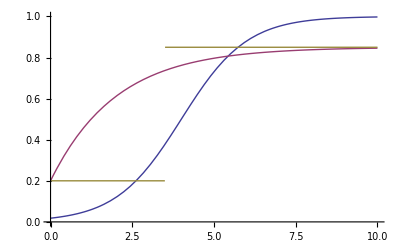

```mathematica
Plot[{logistic[x,{4,1}],bkt[x,{.5,.2,.15}],step[x,{4,.2,.15}]},{x,0,10},PlotRange->{0,1}]
```

```mathematica
stepFit[data_]:=Block[{best=-Infinity,lBest},Do[Block[{l0=Count[Take[data,i],0,1],l1=Count[Take[data,i],1,1],u0=Count[Drop[data,i],0,1],u1=Count[Drop[data,i],1,1],g,s,logLike=0},If[l0+l1>0,g=l1/(l0+l1);logLike+=If[l1>0,l1*Log[g],0]+If[l0>0,l0*Log[1-g],0]];If[u0+u1>0,s=u0/(u0+u1);logLike+=If[u0>0,u0*Log[s],0]+If[u1>0,u1*Log[1-s],0]];
	(*Print[{i,g,s,logLike}]; *)If[logLike>best,best=logLike;lBest=i]],{i,0,Length[data]-1}];If[Length[data]≥3,2*3-2*N[best]]]
```

```mathematica
TableForm[Map[{#[[1]],stepFit[Drop[#,3]]}&,data]]
```

accel-constant-speed | Null
area-of-circle | Null
bernoulli | 6.
combo-magnification | Null
compo-general-case | 32.9921
compo-general-case-unknown | Null
compo-parallel-axis | 82.3817
compo-perpendicular | 39.1042
compo-z-axis | 16.585
compo-zero-vector | Null
continuity | Null
define-angle-between-lines | 6.
define-angular-frequency | 9.81909
define-area | Null
define-area-at | Null
define-charge | 28.4934
define-coef-friction | Null
define-compression | Null
define-current-thru | 17.4573
define-distance | 6.
define-distance-between | 9.81909
define-duration | 21.2763
define-electric-power-var | 6.
define-energy-var | Null
define-flux | Null
define-focal-length | 6.
define-frequency | 20.0453
define-grav-accel | 6.
define-image-distance | 8.77259
define-index-of-refraction | 6.
define-magnification | 6.
define-mass | 18.3152
define-mass-density | 6.
define-moment-of-inertia | 6.
define-object-distance | 6.
define-period-var | 8.77259
define-pressure | 15.5607
define-radius-of-circle | 6.
define-resistance-var | 14.9974
define-revolution-radius | 6.
define-shape-length | 6.
define-slit-separation | Null
define-speed | 8.77259
define-spring-constant | 8.77259
define-stored-energy-var | Null
define-turns | Null
define-voltage-across | 23.1989
define-volume | Null
define-wavelength | 6.
define-work | 8.77259
definition-syntax | 6.
draw-accel-free-fall | 6.
draw-accel-slow-down | Null
draw-accel-speed-up | 13.6382
draw-ang-accel | Null
draw-ang-accel-speed-up | Null
draw-ang-displacement-unknown | Null
draw-ang-momentum-rotating | 6.
draw-ang-velocity-rotating | 6.
draw-applied-force | 6.
draw-bfield-straight-current | 8.77259
draw-bforce-charge | 6.
draw-bforce-rhr-zero | Null
draw-bforce-unknown-velocity | Null
draw-body | 63.6435
draw-buoyant-force | Null
draw-centripetal-acceleration | 8.77259
draw-compo-form-axes | 17.4573
draw-coulomb-force-unknown | 6.
draw-displacement-given-dir | 8.77259
draw-displacement-straight | 10.4987
draw-displacement-unknown | Null
draw-displacement-zero | Null
draw-electric-force-given-field-dir | Null
draw-electric-force-given-field-unknown | Null
draw-energy-axes | 6.
draw-field-given-dir | 9.81909
draw-field-unknown | Null
draw-grav-force | Null
draw-impulse-given-momenta | Null
draw-kinetic-friction | Null
draw-line-given-dir | 13.6382
draw-line-unknown-dir | 6.
draw-momentum-at-rest | Null
draw-momentum-straight | 13.6382
draw-net-field-given-dir | 6.
draw-net-field-given-zero | Null
draw-net-field-unknown | Null
draw-net-force-from-accel | Null
draw-net-force-from-forces | Null
draw-net-force-unknown | Null
draw-normal | 10.4987
draw-point-efield-unknown | Null
draw-projection-axes | 6.
draw-relative-position | 8.77259
draw-relative-position-unknown | 6.
draw-spring-force | Null
draw-tension | 15.5607
draw-torque | Null
draw-unrotated-axes | 25.8748
draw-vector-aligned-axes | 6.
draw-velocity-at-rest | 9.81909
draw-velocity-curved | 14.9974
draw-velocity-curved-unknown | Null
draw-velocity-momentarily-at-rest | 10.4987
draw-velocity-straight | 39.5434
draw-velocity-straight-unknown | Null
draw-weight | 17.1624
draw-xy-vector-given-compos | Null
draw-z-axis-vector-given-compos | Null
equation-syntax | 30.356
equiv-resistance-parallel | 9.81909
equiv-resistance-series | 6.
kinetic-friction-law | Null
lens-combo | Null
lens-eqn | 9.81909
magnification-eqn | 6.
object-label | 6.
pendulum-oscillation | Null
pressure-at-open-to-atmosphere | 6.
pressure-force | Null
pressure-height-fluid | Null
sdd-constvel-compo | 9.81909
select-mc-answer | 65.5343
spring-law-compression | Null
spring-mass-oscillation | Null
write-ang-momentum | 6.
write-angle-direction-known-lines | 6.
write-archimedes | Null
write-average-rate-of-change | Null
write-cap-energy | Null
write-capacitance-definition | 6.
write-centripetal-accel | 6.
write-change-me | Null
write-charge-force-bfield | 8.77259
write-charge-force-bfield-mag | Null
write-charge-force-efield-compo | 6.
write-charge-force-efield-mag | Null
write-charge-same-caps-in-branch | Null
write-connected-accels | Null
write-cons-angmom | Null
write-cons-linmom-compo-join-split | Null
write-coulomb | Null
write-coulomb-compo | 6.
write-density | Null
write-electric-power | 8.77259
write-energy-cons | 6.
write-equality | 6.
write-faradays-law | Null
write-flux-constant-field | Null
write-flux-zero | Null
write-free-fall-accel | 6.
write-g-on-earth | Null
write-grav-energy | 11.004
write-harmonic-of | 6.
write-height-dy | Null
write-i-hoop-cm | Null
write-impulse-compo | Null
write-impulse-momentum-compo | Null
write-inside-solenoid-bfield | Null
write-junction-rule | Null
write-junction-rule-cap | Null
write-kinetic-energy | 15.5607
write-known-value-eqn | 235.968
write-linear-vel | Null
write-lk-no-s-compo | 14.3758
write-lk-no-t-compo | Null
write-lk-no-vf-compo | 10.4987
write-loop-rule-capacitors | 11.7416
write-loop-rule-resistors | 10.4987
write-mag-torque | Null
write-mass-compound | Null
write-momentum-compo | 6.
write-net-field-compo | Null
write-net-force-compo | 9.81909
write-nfl-compo | 12.7301
write-nsl-compo | 21.0257
write-nsl-rot-compo | Null
write-null-spring-energy | Null
write-ohms-law | 17.2868
write-period-circular | Null
write-point-charge-efield-compo | 6.
write-potential-energy | Null
write-right-triangle-tangent | Null
write-rk-no-s | Null
write-rk-no-vf | Null
write-sdd | 8.77259
write-single-loop-rule | Null
write-slit-interference | 6.
write-snells-law | Null
write-spring-energy | 8.77259
write-straight-wire-bfield | Null
write-sum-disp-compo | Null
write-sum-times | Null
write-tensions-equal | 6.
write-total-energy-top | 15.5607
write-transformer-power | Null
write-turns-per-length | Null
write-ug | Null
write-unit-vector-mag | Null
write-vector-magnitude | 6.
write-wave-speed-light | Null
write-wnc | Null
write-work | 6.
wt-law | 17.4573

```mathematica
logger[x_?NumberQ,params_]:= (* not used now. *)Which[0<x≤1,Log[x],x==0,(* NMaximize can't handle Infinity *)-10^50,True,Print["Invalid probability ",x," for ",params];If[x<0,-Infinity,0]]
logProb[model_,params_,data_]:=Sum[Log[If[data[[i]]==1,model[i-1,params],1-model[i,params]]],{i,Length[data]}]
maxer[model_,vars_,constraints_,data_]:=Which[
(* too few data points *)
Length[data]<Length[vars],Null,
(* All three functions can perfectly fit to all ones or zeros, but numerical fit is hard. *)
Count[data,0,1]==0 || Count[data,1,1]==0,2 Length[vars],True,
Block[{x=NMaximize[{logProb[model,vars,data],constraints[data]},vars,Method->{"RandomSearch",Method->"ConjugateGradient"}]},If[NumberQ[x[[1]]],2Length[vars]-2 x[[1]],Print[data,x];False]]]
```

```mathematica
data[[11]]
```

{continuity,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,1,0}

```mathematica
logisticConstraints[x_]:=Block[{delta=15,ones=Position[x,1,1],zeros=Position[x,0,1]},mu≥Max[zeros[[-1,1]]*b,zeros[[1,1]]*b]-delta&& mu≤Min[ones[[1,1]]*b,ones[[-1,1]]*b]+delta&& b>-2 delta/Max[1,ones[[-1,1]]-zeros[[1,1]]] && b<2 delta/Max[1,zeros[[-1,1]]-ones[[1,1]]]]
```

```mathematica
bktConstraints[_]:=Block[{delta=15},pg≥Exp[-delta] && ps≥Exp[-delta] && pg≤1-Exp[-delta] && ps≤ 1-Exp[-delta] &&b≥0 && b<delta]
```

Add AIC values for all sets with 3 or more points

```mathematica
aics=Apply[Plus,Map[If[Length[Drop[#,3]]≥3,{maxer[logistic,{mu,b},logisticConstraints,Drop[#,3]],maxer[bkt,{b,pg,ps},bktConstraints,Drop[#,3]],stepFit[Drop[#,3]]},0]&,data]]
```

Experimental`NumericalFunction::nnum: The function value Indeterminate is not a number at {b, mu} = {-30., -232.516}.

General::stop: Further output of Experimental`NumericalFunction :: nnum will be suppressed during this calculation.

{1540.5,1781.08,1567.25}

```mathematica
TableForm[Map[{#[[1]],Print[#[[1]]," logistic"];maxer[logistic,{mu,b},logisticConstraints,Drop[#,3]],Print[#[[1]]," bkt"];maxer[bkt,{b,pg,ps},bktConstraints,Drop[#,3]],stepFit[Drop[#,3]]}&,data]]
```

accel-constant-speed logistic

accel-constant-speed bkt

area-of-circle logistic

area-of-circle bkt

bernoulli logistic

bernoulli bkt

combo-magnification logistic

combo-magnification bkt

compo-general-case logistic

compo-general-case bkt

compo-general-case-unknown logistic

compo-general-case-unknown bkt

compo-parallel-axis logistic

compo-parallel-axis bkt

compo-perpendicular logistic

compo-perpendicular bkt

compo-z-axis logistic

compo-z-axis bkt

compo-zero-vector logistic

compo-zero-vector bkt

continuity logistic

continuity bkt

define-angle-between-lines logistic

define-angle-between-lines bkt

define-angular-frequency logistic

define-angular-frequency bkt

define-area logistic

define-area bkt

define-area-at logistic

define-area-at bkt

define-charge logistic

define-charge bkt

define-coef-friction logistic

define-coef-friction bkt

define-compression logistic

define-compression bkt

define-current-thru logistic

define-current-thru bkt

define-distance logistic

define-distance bkt

define-distance-between logistic

define-distance-between bkt

define-duration logistic

define-duration bkt

define-electric-power-var logistic

define-electric-power-var bkt

define-energy-var logistic

define-energy-var bkt

define-flux logistic

define-flux bkt

define-focal-length logistic

define-focal-length bkt

define-frequency logistic

define-frequency bkt

define-grav-accel logistic

define-grav-accel bkt

define-image-distance logistic

define-image-distance bkt

define-index-of-refraction logistic

define-index-of-refraction bkt

define-magnification logistic

Experimental`NumericalFunction::nnum: The function value Indeterminate is not a number at {b, mu} = {-30., -232.516}.

General::stop: Further output of Experimental`NumericalFunction :: nnum will be suppressed during this calculation.

define-magnification bkt

define-mass logistic

define-mass bkt

define-mass-density logistic

define-mass-density bkt

define-moment-of-inertia logistic

define-moment-of-inertia bkt

define-object-distance logistic

define-object-distance bkt

define-period-var logistic

define-period-var bkt

define-pressure logistic

define-pressure bkt

define-radius-of-circle logistic

define-radius-of-circle bkt

define-resistance-var logistic

define-resistance-var bkt

define-revolution-radius logistic

define-revolution-radius bkt

define-shape-length logistic

define-shape-length bkt

define-slit-separation logistic

define-slit-separation bkt

define-speed logistic

define-speed bkt

define-spring-constant logistic

define-spring-constant bkt

define-stored-energy-var logistic

define-stored-energy-var bkt

define-turns logistic

define-turns bkt

define-voltage-across logistic

define-voltage-across bkt

define-volume logistic

define-volume bkt

define-wavelength logistic

define-wavelength bkt

define-work logistic

define-work bkt

definition-syntax logistic

definition-syntax bkt

draw-accel-free-fall logistic

draw-accel-free-fall bkt

draw-accel-slow-down logistic

draw-accel-slow-down bkt

draw-accel-speed-up logistic

draw-accel-speed-up bkt

draw-ang-accel logistic

draw-ang-accel bkt

draw-ang-accel-speed-up logistic

draw-ang-accel-speed-up bkt

draw-ang-displacement-unknown logistic

draw-ang-displacement-unknown bkt

draw-ang-momentum-rotating logistic

draw-ang-momentum-rotating bkt

draw-ang-velocity-rotating logistic

draw-ang-velocity-rotating bkt

draw-applied-force logistic

draw-applied-force bkt

draw-bfield-straight-current logistic

draw-bfield-straight-current bkt

draw-bforce-charge logistic

draw-bforce-charge bkt

draw-bforce-rhr-zero logistic

draw-bforce-rhr-zero bkt

draw-bforce-unknown-velocity logistic

draw-bforce-unknown-velocity bkt

draw-body logistic

draw-body bkt

draw-buoyant-force logistic

draw-buoyant-force bkt

draw-centripetal-acceleration logistic

draw-centripetal-acceleration bkt

draw-compo-form-axes logistic

draw-compo-form-axes bkt

draw-coulomb-force-unknown logistic

draw-coulomb-force-unknown bkt

draw-displacement-given-dir logistic

draw-displacement-given-dir bkt

draw-displacement-straight logistic

draw-displacement-straight bkt

draw-displacement-unknown logistic

draw-displacement-unknown bkt

draw-displacement-zero logistic

draw-displacement-zero bkt

draw-electric-force-given-field-dir logistic

draw-electric-force-given-field-dir bkt

draw-electric-force-given-field-unknown logistic

draw-electric-force-given-field-unknown bkt

draw-energy-axes logistic

draw-energy-axes bkt

draw-field-given-dir logistic

draw-field-given-dir bkt

draw-field-unknown logistic

draw-field-unknown bkt

draw-grav-force logistic

draw-grav-force bkt

draw-impulse-given-momenta logistic

draw-impulse-given-momenta bkt

draw-kinetic-friction logistic

draw-kinetic-friction bkt

draw-line-given-dir logistic

draw-line-given-dir bkt

draw-line-unknown-dir logistic

draw-line-unknown-dir bkt

draw-momentum-at-rest logistic

draw-momentum-at-rest bkt

draw-momentum-straight logistic

draw-momentum-straight bkt

draw-net-field-given-dir logistic

draw-net-field-given-dir bkt

draw-net-field-given-zero logistic

draw-net-field-given-zero bkt

draw-net-field-unknown logistic

draw-net-field-unknown bkt

draw-net-force-from-accel logistic

draw-net-force-from-accel bkt

draw-net-force-from-forces logistic

draw-net-force-from-forces bkt

draw-net-force-unknown logistic

draw-net-force-unknown bkt

draw-normal logistic

draw-normal bkt

draw-point-efield-unknown logistic

draw-point-efield-unknown bkt

draw-projection-axes logistic

draw-projection-axes bkt

draw-relative-position logistic

draw-relative-position bkt

draw-relative-position-unknown logistic

draw-relative-position-unknown bkt

draw-spring-force logistic

draw-spring-force bkt

draw-tension logistic

draw-tension bkt

draw-torque logistic

draw-torque bkt

draw-unrotated-axes logistic

draw-unrotated-axes bkt

draw-vector-aligned-axes logistic

draw-vector-aligned-axes bkt

draw-velocity-at-rest logistic

draw-velocity-at-rest bkt

draw-velocity-curved logistic

draw-velocity-curved bkt

draw-velocity-curved-unknown logistic

draw-velocity-curved-unknown bkt

draw-velocity-momentarily-at-rest logistic

draw-velocity-momentarily-at-rest bkt

draw-velocity-straight logistic

draw-velocity-straight bkt

draw-velocity-straight-unknown logistic

draw-velocity-straight-unknown bkt

draw-weight logistic

draw-weight bkt

draw-xy-vector-given-compos logistic

draw-xy-vector-given-compos bkt

draw-z-axis-vector-given-compos logistic

draw-z-axis-vector-given-compos bkt

equation-syntax logistic

equation-syntax bkt

equiv-resistance-parallel logistic

equiv-resistance-parallel bkt

equiv-resistance-series logistic

equiv-resistance-series bkt

kinetic-friction-law logistic

kinetic-friction-law bkt

lens-combo logistic

lens-combo bkt

lens-eqn logistic

lens-eqn bkt

magnification-eqn logistic

magnification-eqn bkt

object-label logistic

object-label bkt

pendulum-oscillation logistic

pendulum-oscillation bkt

pressure-at-open-to-atmosphere logistic

pressure-at-open-to-atmosphere bkt

pressure-force logistic

pressure-force bkt

pressure-height-fluid logistic

pressure-height-fluid bkt

sdd-constvel-compo logistic

sdd-constvel-compo bkt

select-mc-answer logistic

select-mc-answer bkt

spring-law-compression logistic

spring-law-compression bkt

spring-mass-oscillation logistic

spring-mass-oscillation bkt

write-ang-momentum logistic

write-ang-momentum bkt

write-angle-direction-known-lines logistic

write-angle-direction-known-lines bkt

write-archimedes logistic

write-archimedes bkt

write-average-rate-of-change logistic

write-average-rate-of-change bkt

write-cap-energy logistic

write-cap-energy bkt

write-capacitance-definition logistic

write-capacitance-definition bkt

write-centripetal-accel logistic

write-centripetal-accel bkt

write-change-me logistic

write-change-me bkt

write-charge-force-bfield logistic

write-charge-force-bfield bkt

write-charge-force-bfield-mag logistic

write-charge-force-bfield-mag bkt

write-charge-force-efield-compo logistic

write-charge-force-efield-compo bkt

write-charge-force-efield-mag logistic

write-charge-force-efield-mag bkt

write-charge-same-caps-in-branch logistic

write-charge-same-caps-in-branch bkt

write-connected-accels logistic

write-connected-accels bkt

write-cons-angmom logistic

write-cons-angmom bkt

write-cons-linmom-compo-join-split logistic

write-cons-linmom-compo-join-split bkt

write-coulomb logistic

write-coulomb bkt

write-coulomb-compo logistic

write-coulomb-compo bkt

write-density logistic

write-density bkt

write-electric-power logistic

write-electric-power bkt

write-energy-cons logistic

write-energy-cons bkt

write-equality logistic

write-equality bkt

write-faradays-law logistic

write-faradays-law bkt

write-flux-constant-field logistic

write-flux-constant-field bkt

write-flux-zero logistic

write-flux-zero bkt

write-free-fall-accel logistic

write-free-fall-accel bkt

write-g-on-earth logistic

write-g-on-earth bkt

write-grav-energy logistic

write-grav-energy bkt

write-harmonic-of logistic

write-harmonic-of bkt

write-height-dy logistic

write-height-dy bkt

write-i-hoop-cm logistic

write-i-hoop-cm bkt

write-impulse-compo logistic

write-impulse-compo bkt

write-impulse-momentum-compo logistic

write-impulse-momentum-compo bkt

write-inside-solenoid-bfield logistic

write-inside-solenoid-bfield bkt

write-junction-rule logistic

write-junction-rule bkt

write-junction-rule-cap logistic

write-junction-rule-cap bkt

write-kinetic-energy logistic

write-kinetic-energy bkt

write-known-value-eqn logistic

write-known-value-eqn bkt

write-linear-vel logistic

write-linear-vel bkt

write-lk-no-s-compo logistic

write-lk-no-s-compo bkt

write-lk-no-t-compo logistic

write-lk-no-t-compo bkt

write-lk-no-vf-compo logistic

write-lk-no-vf-compo bkt

write-loop-rule-capacitors logistic

write-loop-rule-capacitors bkt

write-loop-rule-resistors logistic

write-loop-rule-resistors bkt

write-mag-torque logistic

write-mag-torque bkt

write-mass-compound logistic

write-mass-compound bkt

write-momentum-compo logistic

write-momentum-compo bkt

write-net-field-compo logistic

write-net-field-compo bkt

write-net-force-compo logistic

write-net-force-compo bkt

write-nfl-compo logistic

write-nfl-compo bkt

write-nsl-compo logistic

write-nsl-compo bkt

write-nsl-rot-compo logistic

write-nsl-rot-compo bkt

write-null-spring-energy logistic

write-null-spring-energy bkt

write-ohms-law logistic

write-ohms-law bkt

write-period-circular logistic

write-period-circular bkt

write-point-charge-efield-compo logistic

write-point-charge-efield-compo bkt

write-potential-energy logistic

write-potential-energy bkt

write-right-triangle-tangent logistic

write-right-triangle-tangent bkt

write-rk-no-s logistic

write-rk-no-s bkt

write-rk-no-vf logistic

write-rk-no-vf bkt

write-sdd logistic

write-sdd bkt

write-single-loop-rule logistic

write-single-loop-rule bkt

write-slit-interference logistic

write-slit-interference bkt

write-snells-law logistic

write-snells-law bkt

write-spring-energy logistic

write-spring-energy bkt

write-straight-wire-bfield logistic

write-straight-wire-bfield bkt

write-sum-disp-compo logistic

write-sum-disp-compo bkt

write-sum-times logistic

write-sum-times bkt

write-tensions-equal logistic

write-tensions-equal bkt

write-total-energy-top logistic

write-total-energy-top bkt

write-transformer-power logistic

write-transformer-power bkt

write-turns-per-length logistic

write-turns-per-length bkt

write-ug logistic

write-ug bkt

write-unit-vector-mag logistic

write-unit-vector-mag bkt

write-vector-magnitude logistic

write-vector-magnitude bkt

write-wave-speed-light logistic

write-wave-speed-light bkt

write-wnc logistic

write-wnc bkt

write-work logistic

write-work bkt

wt-law logistic

wt-law bkt

accel-constant-speed | Null | Null | Null
area-of-circle | 6.77259 | Null | Null
bernoulli | 6.77259 | 9.36506 | 6.
combo-magnification | Null | Null | Null
compo-general-case | 34.4483 | 36.4727 | 32.9921
compo-general-case-unknown | Null | Null | Null
compo-parallel-axis | 84.0896 | 86.0307 | 82.3817
compo-perpendicular | 41.4331 | 41.7105 | 39.1042
compo-z-axis | 16.6739 | 17.6964 | 16.585
compo-zero-vector | Null | Null | Null
continuity | 4. | Null | Null
define-angle-between-lines | 4 | 6 | 6.
define-angular-frequency | 9.54518 | 11.5452 | 9.81909
define-area | Null | Null | Null
define-area-at | 4 | Null | Null
define-charge | 28.695 | 30.8353 | 28.4934
define-coef-friction | Null | Null | Null
define-compression | 4 | Null | Null
define-current-thru | 19.0189 | 21.1677 | 17.4573
define-distance | 6.77259 | 10.3095 | 6.
define-distance-between | 9.00018 | 11.2477 | 9.81909
define-duration | 23.2515 | 25.3179 | 21.2763
define-electric-power-var | 6.77259 | 9.30902 | 6.
define-energy-var | Null | Null | Null
define-flux | 6.77259 | Null | Null
define-focal-length | 6.77259 | 10.3095 | 6.
define-frequency | 23.7034 | 24.5515 | 20.0453
define-grav-accel | 4 | 6 | 6.
define-image-distance | 6.77259 | 9.8176 | 8.77259
define-index-of-refraction | 4 | 6 | 6.
define-magnification | 4. | 8.39018 | 6.
define-mass | 18.5006 | 21.0897 | 18.3152
define-mass-density | 6.77259 | 9.34037 | 6.
define-moment-of-inertia | 6.77259 | 9.30902 | 6.
define-object-distance | 6.77259 | 9.30902 | 6.
define-period-var | 8.42532 | 9.81909 | 8.77259
define-pressure | 17.3586 | 20.0784 | 15.5607
define-radius-of-circle | 6.77259 | 9.20179 | 6.
define-resistance-var | 14.1052 | 16.8047 | 14.9974
define-revolution-radius | 4 | 6 | 6.
define-shape-length | 6.77259 | 9.20179 | 6.
define-slit-separation | 4. | Null | Null
define-speed | 8.97592 | 10.4987 | 8.77259
define-spring-constant | 6.77259 | 8.77259 | 8.77259
define-stored-energy-var | 4 | Null | Null
define-turns | 4 | Null | Null
define-voltage-across | 24.7313 | 26.7277 | 23.1989
define-volume | Null | Null | Null
define-wavelength | 6.77259 | 9.20179 | 6.
define-work | 6.77259 | 8.97779 | 8.77259
definition-syntax | 4 | 6 | 6.
draw-accel-free-fall | 4 | 6 | 6.
draw-accel-slow-down | Null | Null | Null
draw-accel-speed-up | 16.1728 | 17.6611 | 13.6382
draw-ang-accel | Null | Null | Null
draw-ang-accel-speed-up | 4. | Null | Null
draw-ang-displacement-unknown | Null | Null | Null
draw-ang-momentum-rotating | 4 | 6 | 6.
draw-ang-velocity-rotating | 4. | 10.8486 | 6.
draw-applied-force | 4. | 7.84029 | 6.
draw-bfield-straight-current | 6.77259 | 9.8176 | 8.77259
draw-bforce-charge | 4. | 9.30723 | 6.
draw-bforce-rhr-zero | Null | Null | Null
draw-bforce-unknown-velocity | Null | Null | Null
draw-body | 65.2011 | 65.6523 | 63.6435
draw-buoyant-force | Null | Null | Null
draw-centripetal-acceleration | 8.42532 | 9.81909 | 8.77259
draw-compo-form-axes | 17.4741 | 18.6839 | 17.4573
draw-coulomb-force-unknown | 6.77259 | 9.36506 | 6.
draw-displacement-given-dir | 8.97592 | 10.4987 | 8.77259
draw-displacement-straight | 8.98488 | 11.0404 | 10.4987
draw-displacement-unknown | Null | Null | Null
draw-displacement-zero | Null | Null | Null
draw-electric-force-given-field-dir | Null | Null | Null
draw-electric-force-given-field-unknown | Null | Null | Null
draw-energy-axes | 6.77259 | 9.20179 | 6.
draw-field-given-dir | 9.35963 | 10.8774 | 9.81909
draw-field-unknown | Null | Null | Null
draw-grav-force | 4 | Null | Null
draw-impulse-given-momenta | Null | Null | Null
draw-kinetic-friction | 4 | Null | Null
draw-line-given-dir | 15.0904 | 16.5324 | 13.6382
draw-line-unknown-dir | 4 | 6 | 6.
draw-momentum-at-rest | 4 | Null | Null
draw-momentum-straight | 12.9651 | 14.3758 | 13.6382
draw-net-field-given-dir | 4 | 6 | 6.
draw-net-field-given-zero | Null | Null | Null
draw-net-field-unknown | Null | Null | Null
draw-net-force-from-accel | 4. | Null | Null
draw-net-force-from-forces | Null | Null | Null
draw-net-force-unknown | Null | Null | Null
draw-normal | 9.07527 | 11.1218 | 10.4987
draw-point-efield-unknown | 6.77259 | Null | Null
draw-projection-axes | 4 | 6 | 6.
draw-relative-position | 9.19789 | 11.004 | 8.77259
draw-relative-position-unknown | 4. | 9.03164 | 6.
draw-spring-force | 6.77259 | Null | Null
draw-tension | 16.2077 | 17.4573 | 15.5607
draw-torque | Null | Null | Null
draw-unrotated-axes | 26.8119 | 27.5501 | 25.8748
draw-vector-aligned-axes | 4 | 6 | 6.
draw-velocity-at-rest | 8.83443 | 11.0279 | 9.81909
draw-velocity-curved | 15.4573 | 17.262 | 14.9974
draw-velocity-curved-unknown | 4 | Null | Null
draw-velocity-momentarily-at-rest | 9.09918 | 11.6875 | 10.4987
draw-velocity-straight | 39.3955 | 40.6129 | 39.5434
draw-velocity-straight-unknown | Null | Null | Null
draw-weight | 18.3371 | 19.7542 | 17.1624
draw-xy-vector-given-compos | 4. | Null | Null
draw-z-axis-vector-given-compos | 6.77259 | Null | Null
equation-syntax | 31.0029 | 34.2829 | 30.356
equiv-resistance-parallel | 8.83443 | 9.81909 | 9.81909
equiv-resistance-series | 4 | 6 | 6.
kinetic-friction-law | Null | Null | Null
lens-combo | Null | Null | Null
lens-eqn | 9.54518 | 11.5452 | 9.81909
magnification-eqn | 4 | 6 | 6.
object-label | 4 | 6 | 6.
pendulum-oscillation | 4. | Null | Null
pressure-at-open-to-atmosphere | 6.77259 | 9.20179 | 6.
pressure-force | 6.77259 | Null | Null
pressure-height-fluid | Null | Null | Null
sdd-constvel-compo | 8.83443 | 9.81909 | 9.81909
select-mc-answer | 70.8794 | 69.2292 | 65.5343
spring-law-compression | 6.77259 | Null | Null
spring-mass-oscillation | Null | Null | Null
write-ang-momentum | 6.77259 | 9.20179 | 6.
write-angle-direction-known-lines | 6.77259 | 9.36506 | 6.
write-archimedes | Null | Null | Null
write-average-rate-of-change | Null | Null | Null
write-cap-energy | 4 | Null | Null
write-capacitance-definition | 6.77259 | 11.7414 | 6.
write-centripetal-accel | 4. | 7.49956 | 6.
write-change-me | Null | Null | Null
write-charge-force-bfield | 6.77259 | 8.97779 | 8.77259
write-charge-force-bfield-mag | 6.77259 | Null | Null
write-charge-force-efield-compo | 4 | 6 | 6.
write-charge-force-efield-mag | Null | Null | Null
write-charge-same-caps-in-branch | Null | Null | Null
write-connected-accels | 6.77259 | Null | Null
write-cons-angmom | Null | Null | Null
write-cons-linmom-compo-join-split | 4 | Null | Null
write-coulomb | Null | Null | Null
write-coulomb-compo | 6.77259 | 9.30902 | 6.
write-density | Null | Null | Null
write-electric-power | 6.77259 | 9.8176 | 8.77259
write-energy-cons | 4 | 6 | 6.
write-equality | 4 | 6 | 6.
write-faradays-law | Null | Null | Null
write-flux-constant-field | Null | Null | Null
write-flux-zero | Null | Null | Null
write-free-fall-accel | 4 | 6 | 6.
write-g-on-earth | Null | Null | Null
write-grav-energy | 11.1976 | 14.19 | 11.004
write-harmonic-of | 4 | 6 | 6.
write-height-dy | 4. | Null | Null
write-i-hoop-cm | Null | Null | Null
write-impulse-compo | Null | Null | Null
write-impulse-momentum-compo | Null | Null | Null
write-inside-solenoid-bfield | Null | Null | Null
write-junction-rule | Null | Null | Null
write-junction-rule-cap | Null | Null | Null
write-kinetic-energy | 16.0388 | 18.1198 | 15.5607
write-known-value-eqn | 240.13 | 242.237 | 235.968
write-linear-vel | Null | Null | Null
write-lk-no-s-compo | 14.5704 | 16.3798 | 14.3758
write-lk-no-t-compo | 4. | Null | Null
write-lk-no-vf-compo | 8.98488 | 11.0404 | 10.4987
write-loop-rule-capacitors | 12.9635 | 14.4614 | 11.7416
write-loop-rule-resistors | 10.1904 | 10.4987 | 10.4987
write-mag-torque | Null | Null | Null
write-mass-compound | Null | Null | Null
write-momentum-compo | 4. | 9.03164 | 6.
write-net-field-compo | 4 | Null | Null
write-net-force-compo | 11.5044 | 12.7301 | 9.81909
write-nfl-compo | 12.903 | 14.2423 | 12.7301
write-nsl-compo | 23.3678 | 26.3663 | 21.0257
write-nsl-rot-compo | Null | Null | Null
write-null-spring-energy | Null | Null | Null
write-ohms-law | 16.8894 | 18.2173 | 17.2868
write-period-circular | Null | Null | Null
write-point-charge-efield-compo | 6.77259 | 10.3095 | 6.
write-potential-energy | Null | Null | Null
write-right-triangle-tangent | 6.77259 | Null | Null
write-rk-no-s | 4 | Null | Null
write-rk-no-vf | Null | Null | Null
write-sdd | 8.42532 | 9.81909 | 8.77259
write-single-loop-rule | Null | Null | Null
write-slit-interference | 6.77259 | 10.3095 | 6.
write-snells-law | Null | Null | Null
write-spring-energy | 6.77259 | 9.03814 | 8.77259
write-straight-wire-bfield | 6.77259 | Null | Null
write-sum-disp-compo | 4 | Null | Null
write-sum-times | 6.77259 | Null | Null
write-tensions-equal | 4 | 6 | 6.
write-total-energy-top | 14.7214 | 15.5607 | 15.5607
write-transformer-power | Null | Null | Null
write-turns-per-length | Null | Null | Null
write-ug | 6.77259 | Null | Null
write-unit-vector-mag | Null | Null | Null
write-vector-magnitude | 6.77259 | 9.34037 | 6.
write-wave-speed-light | Null | Null | Null
write-wnc | Null | Null | Null
write-work | 4. | 7.49956 | 6.
wt-law | 17.6362 | 21.4354 | 17.4573